## Agent based model drawing two ants at random at any time step

### Model parameters, number of simulations, and initial conditions

```mathematica
αN=1.47;
E0N=0.0944;
```

```mathematica
δN=0.63;
γ0N=1.21;
β0N=.1γ0N;
```

```mathematica
p1=β0N Δt;
p2=γ0N Δt;
p3=δN Δt;
```

```mathematica
Δt=1/15//N;
ΔΔt=Δt/NN;
```

```mathematica
NN=50;
p=2E0N NN^(αN-2);
```

```mathematica
p NN
```

1.18718

```mathematica
Nre=100;
tmax=10;
Nt=Floor[tmax/ΔΔt];
```

```mathematica
S0=Join[{1},Table[0,{i,1,NN-1}]];
A0=Count[S0,0];
I0=Count[S0,1];
R0=Count[S0,2];
```

### Variables

```mathematica
At=Table[A0,{n,1,Nre},{i,1,Nt}];
It=Table[I0,{n,1,Nre},{i,1,Nt}];
Rt=Table[R0,{n,1,Nre},{i,1,Nt}];
```

### For loop

```mathematica
For[k=1,k<Nre+1,k++,

Statet=S0;

For[t=1,t<Nt ,t++,

Statetp1=Statet;

i=RandomInteger[{1,NN}];
j=RandomInteger[{1,NN}];

aux=RandomReal[];
If[And[Unequal[i,j],aux<NN p],

Which[

Statet[[i]]==0,
If[Statet[[j]]==0,
aux=RandomReal[];
If[aux<p2,Statetp1[[i]]=2]],

Statet[[i]]==1,
If[Statet[[j]]==0,
aux=RandomReal[];
If[aux<p1,Statetp1[[i]]=0]],

Statet[[i]]==2,
aux=RandomReal[];
If[aux<p3,Statetp1[[i]]=1]

],

Statetp1[[i]]=Statet[[i]];
];



At[[k,t+1]]=Count[Statetp1,0];
It[[k,t+1]]=Count[Statetp1,1];
Rt[[k,t+1]]=Count[Statetp1,2];

Statet=Statetp1;

];

]
```

### Plots

```mathematica
A0ssLim=Sqrt[δN/(γ0N 2E0N)]NN^(3/2-αN/2)
R0ssLim=NN
I0ssLim=(Sqrt[γ0N δN/(2E0N)])/β0N NN^((3/2-αN/2))
```

33.1122

50

331.122

```mathematica
t=.
sol=NDSolve[{A'[t]==β0N 2E0N A[t]II[t]NN^(αN-2)-γ0N 2E0N(A[t]^2)NN^(αN-2),II'[t]==δN R[t]-β0N 2E0N II[t] A[t] NN^(αN-2),R'[t]==-δN R[t]+γ0N 2E0N(A[t]^2)NN^(αN-2),A[0]==A0,II[0]==I0,R[0]==R0},{A,II,R},{t,ΔΔt Nt}];
```

```mathematica
AtAvg=Mean[At]//N;
AtStd=StandardDeviation[At]//N;
ItAvg=Mean[It]//N;
ItStd=StandardDeviation[It]//N;
RtAvg=Mean[Rt]//N;
RtStd=StandardDeviation[Rt]//N;
```

```mathematica
PlotNetA=ListLinePlot[{Table[{(t-1) ΔΔt,AtAvg[[t]]/NN},{t,1, Nt}],Table[{(t-1) ΔΔt,(AtAvg[[t]]+AtStd[[t]])/NN},{t,1,Nt}],Table[{(t-1) ΔΔt,(AtAvg[[t]]-AtStd[[t]])/NN},{t,1, Nt}]},PlotRange->{All,{0,1}},PlotStyle->{Orange,None,None},Filling->{1->{2},1->{3}},Frame->True,FrameLabel->{"t[s]","A/N"},AspectRatio->.6,ImageSize->167];
```

```mathematica
PlotA=Plot[Evaluate[(A[t]/NN)/. sol],{t,0,ΔΔt Nt},PlotRange->{All,{0,1}},PlotStyle->{Orange,Dashed},Frame->True,FrameLabel->{"t[s]","A/N"},AspectRatio->.6,ImageSize->167];
```

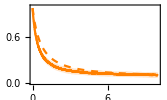

```mathematica
Figa=Show[PlotNetA,PlotA]
```

```mathematica
PlotNetI=ListLinePlot[{Table[{(t-1) ΔΔt,ItAvg[[t]]/NN},{t,1,Nt}],Table[{(t-1) ΔΔt,(ItAvg[[t]]+ItStd[[t]])/NN},{t,1,Nt}],Table[{(t-1) ΔΔt,(ItAvg[[t]]-ItStd[[t]])/NN},{t,1,Nt}]},PlotRange->{All,{0,1}},PlotStyle->{Green,None,None},Filling->{1->{2},1->{3}},Frame->True,FrameLabel->{"t[s]","I/N"},AspectRatio->.6,ImageSize->167];
```

```mathematica
PlotI=Plot[Evaluate[(II[t]/NN)/. sol],{t,0,ΔΔt Nt},PlotRange->{All,{0,1}},PlotStyle->{Green,Dashed},Frame->True,FrameLabel->{"t[s]","I/N"},AspectRatio->.6,ImageSize->167];
```

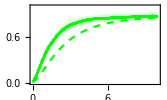

```mathematica
Figb=Show[PlotNetI,PlotI]
```

```mathematica
PlotNetR=ListLinePlot[{Table[{(t-1) ΔΔt,RtAvg[[t]]/NN},{t,1,Nt}],Table[{(t-1) ΔΔt,(RtAvg[[t]]+RtStd[[t]])/NN},{t,1,Nt}],Table[{(t-1) ΔΔt,(RtAvg[[t]]-RtStd[[t]])/NN},{t,1,Nt}]},PlotRange->{All,{0,1}},PlotStyle->{Black,None,None},Filling->{1->{2},1->{3}},Frame->True,FrameLabel->{"t[s]","R/N"},AspectRatio->.6,ImageSize->167];
```

```mathematica
PlotR=Plot[Evaluate[(R[t]/NN)/. sol],{t,0,ΔΔt Nt},PlotRange->{All,{0,1}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"t[s]","R/N"},AspectRatio->.3,ImageSize->167];
```

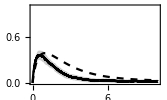

```mathematica
Figc=Show[PlotNetR,PlotR]
```

### Exporting, run one by one

```mathematica
Export["FigL3a.png",Figa];
Export["FigL3b.png",Figb];
Export["FigL3c.png",Figc];
```